## Definitions and setup

```mathematica
hbarc = 0.197326938; (* GeV fm *)
```

```mathematica
wd =SetDirectory@NotebookDirectory[]
```

/Users/mstrickland/Documents/code/qtraj-nlo/mathematica

## Plot setup

```mathematica
myImageSize=450;
```

```mathematica
SetOptions[Plot,Frame->True,Axes->False,ImageSize->myImageSize,AspectRatio->0.75,BaseStyle->18,FrameStyle->AbsoluteThickness[1]];
SetOptions[ListPlot,Frame->True,Axes->False,ImageSize->myImageSize,AspectRatio->0.75,BaseStyle->18,FrameStyle->AbsoluteThickness[1]];
SetOptions[ListLogPlot,Frame->True,Axes->False,ImageSize->myImageSize,AspectRatio->0.75,BaseStyle->18,FrameStyle->AbsoluteThickness[1]];
```

## Glauber stuff

```mathematica
bVals = {"0","2.32326","4.24791","6.00746","7.77937","9.21228","10.4493","11.5541","12.5619","13.4945","14.3815"}//ToExpression;
impactParams = ToString /@ bVals
```

{0,2.32326,4.24791,6.00746,7.77937,9.21228,10.4493,11.5541,12.5619,13.4945,14.3815}

```mathematica
(* This was computed externally for a 5.023 TeV PB-PB collision with sigmaNN = 62 *)
nPartVals={406.12232235261763,374.9882778251423,315.8591222901291,243.53796282970384,168.50283662224285,112.39007027735359,70.7871426138262,41.05093670919672,21.292761520545895,9.667790836200798,3.8095328022884103};
```

```mathematica
Transpose[{bVals,nPartVals}]
```

{{0,406.122},{2.32326,374.988},{4.24791,315.859},{6.00746,243.538},{7.77937,168.503},{9.21228,112.39},{10.4493,70.7871},{11.5541,41.0509},{12.5619,21.2928},{13.4945,9.66779},{14.3815,3.80953}}

```mathematica
nPartVsBInt = Interpolation[Transpose[{bVals,nPartVals}]];
```

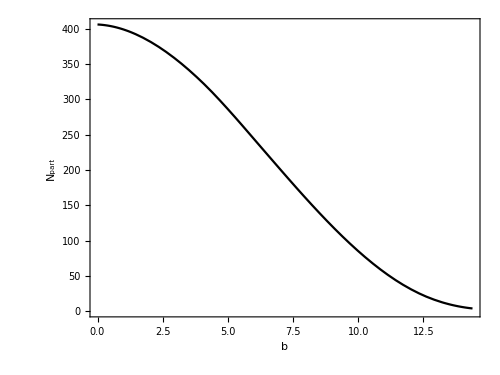

```mathematica
Plot[nPartVsBInt[b],{b,bVals[[1]],bVals[[-1]]},PlotStyle->Black,FrameLabel->{"b","N_part"}]
```

```mathematica
bvscData = Import[wd<>"/input/glauber-data/bvscData.tsv"];
```

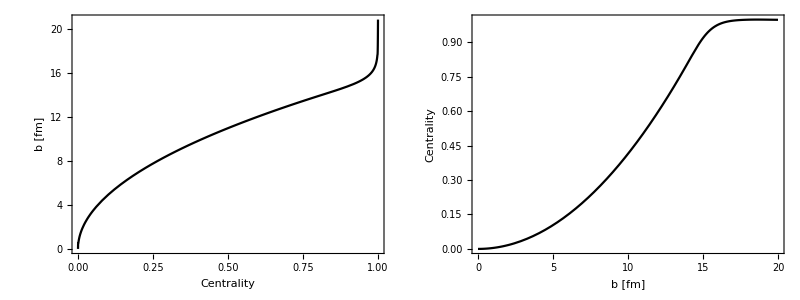

```mathematica
bVsCInt = Interpolation[bvscData];
cVsBInt = Interpolation[Map[Reverse,bvscData]];
Grid[{{Plot[bVsCInt[c],{c,0,1},PlotStyle->Black,FrameLabel->{"Centrality","b [fm]"}],
Plot[cVsBInt[b],{b,0,20},PlotStyle->Black,FrameLabel->{"b [fm]","Centrality"}]}}]
```

```mathematica
cVals=cVsBInt[bVals];
pFunction[c_] = Exp[-c/0.25]/Integrate[Exp[-x/0.25],{x,0,1}]
```

4.07463 ⅇ^(-4. c)

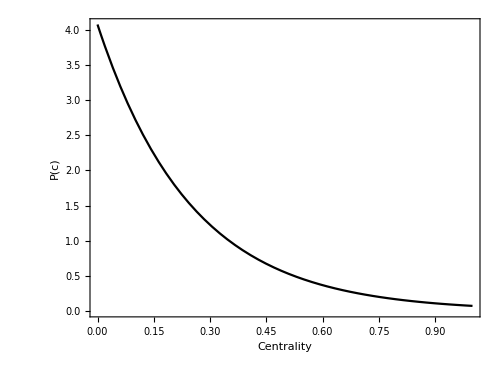

```mathematica
Plot[pFunction[c],{c,0,1},PlotStyle->Black,FrameLabel->{"Centrality","P(c)"}]
```

```mathematica
nbinvsbData = Import[wd<>"/input/glauber-data/nbinvsbData.tsv"];
```

```mathematica
nbinVsb = Interpolation[nbinvsbData]; (* units are fm^2 *)
```

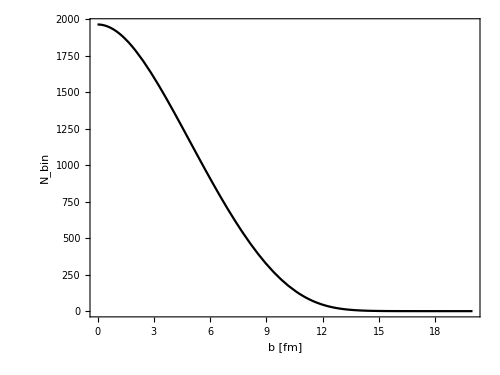

```mathematica
Plot[nbinVsb[b],{b,0,20},PlotStyle->Black,FrameLabel->{"b [fm]","N_bin"}]
```

## Functions

```mathematica
mapVal[x_] := {nPartVsBInt[x[[1]]],x[[2]]}
nPartSort[x_]:=Sort[x,#1[[1]]<#2[[1]]&]
```

```mathematica
computeRAA[ratioData_,state_]:=Module[{data},
Table[
data =ratioData[[i,All,state]];
{bVals[[i]],Around[Mean[data],Max[StandardDeviation[data]/Sqrt[Length[data]],10^(-10)]]},{i,1,Length[impactParams]}]
]
```

```mathematica
computeSwaveRAA[dirs_] := Module[{datafiles,ratioDataRaw,ratioData},
datafiles = Table[Table[wd<>dirs[[j]]<>impactParams[[i]]<>"/ratios.gz",{i,1,Length[impactParams]}],{j,1,Length[dirs]}];
ratioDataRaw= Table[Table[Import[datafiles[[j,i]],"Table"],{i,1,Length[impactParams]}],{j,1,Length[dirs]}];
ratioData = Table[Flatten[Join[Table[ratioDataRaw[[j,i,All]],{j,1,Length[dirs]}]],1],{i,1,Length[impactParams]}];
Table[Join[{{0,1}},nPartSort[mapVal/@computeRAA[ratioData,i]]],{i,{1,2,4}}]
]
```

```mathematica
computePwaveRAA[dirs_] := Module[{datafiles,ratioDataRaw,ratioData},
datafiles = Table[Table[wd<>dirs[[j]]<>impactParams[[i]]<>"/ratios.gz",{i,1,Length[impactParams]}],{j,1,Length[dirs]}];
ratioDataRaw= Table[Table[Import[datafiles[[j,i]]],{i,1,Length[impactParams]}],{j,1,Length[dirs]}];
ratioData = Table[Flatten[Join[Table[ratioDataRaw[[j,i,All]],{j,1,Length[dirs]}]],1],{i,1,Length[impactParams]}];
Table[nPartSort[mapVal/@computeRAA[ratioData,i]],{i,{3,5}}]
]
```

## Compute RAA

#### KCGU - 250

```mathematica
resSwave0 = computeSwaveRAA[{"/input/kcgu/output-FFT/"}]
resSwave1 = computeSwaveRAA[{"/input/kcgu/output-LO/"}]
resSwave2 = computeSwaveRAA[{"/input/kcgu/output-NLO/"}]
```

({3.80953,1.0000000000010} | {9.66779,1.0000000000010} | {21.2928,0.980.04} | {41.0509,1.110.15} | {70.7871,0.780.05} | {112.39,0.6370.020} | {168.503,0.6360.017} | {243.538,0.5390.016} | {315.859,0.4700.014} | {374.988,0.4480.013} | {406.122,0.4380.013}
{3.80953,1.0000000000010} | {9.66779,1.0000000000010} | {21.2928,0.960.04} | {41.0509,0.780.10} | {70.7871,0.2600.018} | {112.39,0.0690.005} | {168.503,0.0430.006} | {243.538,0.0390.005} | {315.859,0.0460.005} | {374.988,0.03770.0034} | {406.122,0.0430.004}
{3.80953,1.0000000000010} | {9.66779,1.0000000000010} | {21.2928,0.960.04} | {41.0509,0.740.10} | {70.7871,0.2260.016} | {112.39,0.0630.004} | {168.503,0.0420.005} | {243.538,0.0330.004} | {315.859,0.0340.004} | {374.988,0.02690.0026} | {406.122,0.03040.0032})

({3.80953,1.0000000000010} | {9.66779,1.0000000000010} | {21.2928,0.98990.0026} | {41.0509,0.8950.009} | {70.7871,0.7600.011} | {112.39,0.6820.011} | {168.503,0.6020.010} | {243.538,0.5410.010} | {315.859,0.4830.009} | {374.988,0.4570.009} | {406.122,0.4320.009}
{3.80953,1.0000000000010} | {9.66779,1.0000000000010} | {21.2928,0.97220.0026} | {41.0509,0.6310.006} | {70.7871,0.2590.004} | {112.39,0.07590.0028} | {168.503,0.03880.0035} | {243.538,0.04120.0031} | {315.859,0.04440.0032} | {374.988,0.04030.0028} | {406.122,0.04750.0034}
{3.80953,1.0000000000010} | {9.66779,1.0000000000010} | {21.2928,0.96920.0026} | {41.0509,0.5960.006} | {70.7871,0.22680.0032} | {112.39,0.06880.0025} | {168.503,0.03800.0027} | {243.538,0.03380.0024} | {315.859,0.03260.0023} | {374.988,0.02820.0020} | {406.122,0.03420.0025})

({3.80953,1.0000000000010} | {9.66779,1.0000000000010} | {21.2928,1.00220.0028} | {41.0509,0.9540.009} | {70.7871,0.9260.012} | {112.39,0.8710.012} | {168.503,0.8480.012} | {243.538,0.8090.012} | {315.859,0.7720.012} | {374.988,0.7730.012} | {406.122,0.7470.012}
{3.80953,1.0000000000010} | {9.66779,1.0000000000010} | {21.2928,0.99720.0028} | {41.0509,0.8520.008} | {70.7871,0.6350.008} | {112.39,0.3830.006} | {168.503,0.2320.005} | {243.538,0.1310.005} | {315.859,0.0860.004} | {374.988,0.0760.005} | {406.122,0.0670.005}
{3.80953,1.0000000000010} | {9.66779,1.0000000000010} | {21.2928,0.99650.0028} | {41.0509,0.8320.008} | {70.7871,0.5750.007} | {112.39,0.2980.004} | {168.503,0.1520.004} | {243.538,0.07200.0028} | {315.859,0.04620.0026} | {374.988,0.03810.0027} | {406.122,0.03600.0027})

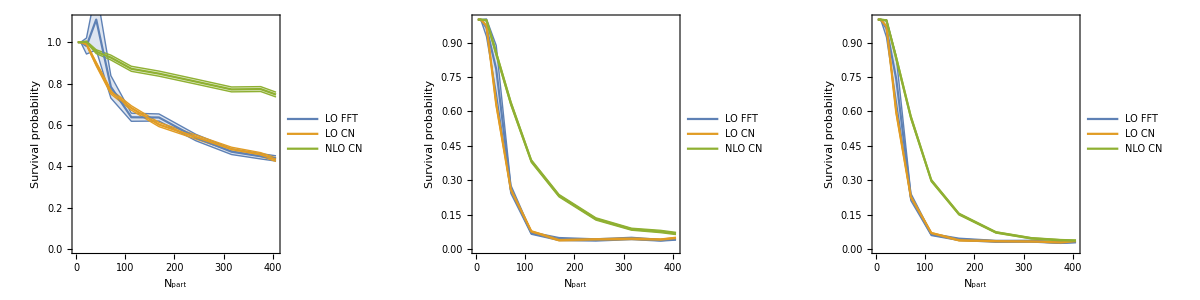

```mathematica
p1=ListPlot[{resSwave0[[1]],resSwave1 [[1]],resSwave2[[1]]},Joined->True,IntervalMarkers->"Bands",PlotLegends->Placed[LineLegend[{"LO FFT","LO CN","NLO CN"},LegendMargins->20,LabelStyle->16],{Right,Top}],FrameLabel->{"N_part","Survival probability"}];
p2=ListPlot[{resSwave0[[2]],resSwave1 [[2]],resSwave2[[2]]},Joined->True,IntervalMarkers->"Bands",PlotLegends->Placed[LineLegend[{"LO FFT","LO CN","NLO CN"},LegendMargins->20,LabelStyle->16],{Right,Top}],FrameLabel->{"N_part","Survival probability"}];
p3=ListPlot[{resSwave0[[3]],resSwave1 [[3]],resSwave2[[3]]},Joined->True,IntervalMarkers->"Bands",PlotLegends->Placed[LineLegend[{"LO FFT","LO CN","NLO CN"},LegendMargins->20,LabelStyle->16],{Right,Top}],FrameLabel->{"N_part","Survival probability"}];
Grid[{{p1,p2,p3}}]
```

#### KCGC - 250

```mathematica
resSwave0 = computeSwaveRAA[{"/input/kcgc/output-v1/"}]
resSwave1 = computeSwaveRAA[{"/input/kcgc/output-LO/"}]
resSwave2 = computeSwaveRAA[{"/input/kcgc/output-NLO/"}]
```

{{{0,1},{3.80953,1.0000000000010},{9.66779,1.0000000000010},{21.2928,0.9810.004},{41.0509,0.8380.013},{70.7871,0.7040.015},{112.39,0.5880.014},{168.503,0.4970.013},{243.538,0.3870.012},{315.859,0.3150.011},{374.988,0.3010.011},{406.122,0.3050.011}},{{0,1},{3.80953,1.0000000000010},{9.66779,1.0000000000010},{21.2928,0.9600.004},{41.0509,0.5680.009},{70.7871,0.2550.005},{112.39,0.10770.0028},{168.503,0.05830.0020},{243.538,0.03740.0015},{315.859,0.03120.0017},{374.988,0.03090.0020},{406.122,0.02770.0015}},{{0,1},{3.80953,1.0000000000010},{9.66779,1.0000000000010},{21.2928,0.9560.004},{41.0509,0.5330.008},{70.7871,0.2170.004},{112.39,0.08080.0023},{168.503,0.03960.0017},{243.538,0.02420.0013},{315.859,0.02050.0015},{374.988,0.02080.0019},{406.122,0.01750.0013}}}

{{{0,1},{3.80953,1.0000000000010},{9.66779,1.0000000000010},{21.2928,0.9850.004},{41.0509,0.8230.012},{70.7871,0.7050.015},{112.39,0.5910.014},{168.503,0.4620.013},{243.538,0.4230.012},{315.859,0.3580.011},{374.988,0.3270.011},{406.122,0.2940.010}},{{0,1},{3.80953,1.0000000000010},{9.66779,1.0000000000010},{21.2928,0.9640.004},{41.0509,0.5580.008},{70.7871,0.2560.005},{112.39,0.10530.0026},{168.503,0.05750.0024},{243.538,0.04250.0020},{315.859,0.03500.0016},{374.988,0.03220.0019},{406.122,0.02900.0018}},{{0,1},{3.80953,1.0000000000010},{9.66779,1.0000000000010},{21.2928,0.9600.004},{41.0509,0.5230.008},{70.7871,0.2170.004},{112.39,0.07830.0020},{168.503,0.04000.0021},{243.538,0.02750.0018},{315.859,0.02320.0015},{374.988,0.02150.0018},{406.122,0.01940.0016}}}

{{{0,1},{3.80953,1.0000000000010},{9.66779,1.0000000000010},{21.2928,0.9940.004},{41.0509,0.9190.012},{70.7871,0.8230.015},{112.39,0.7560.016},{168.503,0.6940.016},{243.538,0.6130.015},{315.859,0.5830.015},{374.988,0.5420.014},{406.122,0.5420.014}},{{0,1},{3.80953,1.0000000000010},{9.66779,1.0000000000010},{21.2928,0.9840.004},{41.0509,0.7500.010},{70.7871,0.4490.008},{112.39,0.2400.005},{168.503,0.12720.0030},{243.538,0.07250.0022},{315.859,0.05330.0017},{374.988,0.04500.0016},{406.122,0.04260.0015}},{{0,1},{3.80953,1.0000000000010},{9.66779,1.0000000000010},{21.2928,0.9830.004},{41.0509,0.7260.010},{70.7871,0.4110.007},{112.39,0.2050.004},{168.503,0.10170.0025},{243.538,0.05450.0018},{315.859,0.03820.0014},{374.988,0.03190.0014},{406.122,0.03000.0014}}}

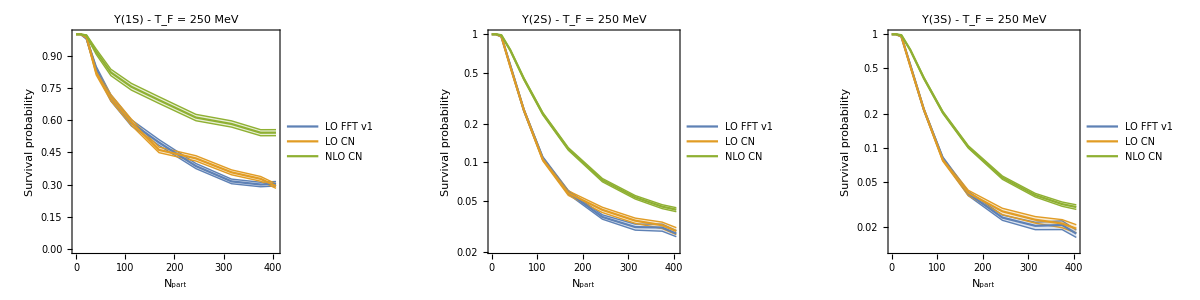

```mathematica
p1=ListPlot[{resSwave0 [[1]],resSwave1[[1]],resSwave2 [[1]]},Joined->True,IntervalMarkers->"Bands",PlotLegends->Placed[LineLegend[{"LO FFT v1","LO CN","NLO CN"},LegendMargins->20,LabelStyle->16],{Right,Top}],FrameLabel->{"N_part","Survival probability"},PlotLabel->Style["Υ(1S) - T_F = 250 MeV",18]];
p2=ListLogPlot[{resSwave0[[2]],resSwave1[[2]],resSwave2[[2]]},Joined->True,IntervalMarkers->"Bands",PlotLegends->Placed[LineLegend[{"LO FFT v1","LO CN","NLO CN"},LegendMargins->20,LabelStyle->16],{Right,Top}],FrameLabel->{"N_part","Survival probability"},PlotLabel->Style["Υ(2S) - T_F = 250 MeV",18]];
p3=ListLogPlot[{resSwave0[[3]],resSwave1[[3]],resSwave2[[3]]},Joined->True,IntervalMarkers->"Bands",PlotLegends->Placed[LineLegend[{"LO FFT v1","LO CN","NLO CN"},LegendMargins->20,LabelStyle->16],{Right,Top}],FrameLabel->{"N_part","Survival probability"},PlotLabel->Style["Υ(3S) - T_F = 250 MeV",18]];
Grid[{{p1,p2,p3}}]
```

#### KCGC - 190

```mathematica
resSwave0190 = computeSwaveRAA[{"/input/kcgc-190/output-v1/"}]
resSwave1190  = computeSwaveRAA[{"/input/kcgc-190/output-LO/"}]
resSwave2190  = computeSwaveRAA[{"/input/kcgc-190/output-NLO/"}]
```

{{{0,1},{3.80953,1.0000000000010},{9.66779,0.9300.010},{21.2928,0.7860.015},{41.0509,0.6960.016},{70.7871,0.5760.015},{112.39,0.4490.013},{168.503,0.3520.011},{243.538,0.2940.011},{315.859,0.2460.010},{374.988,0.2230.009},{406.122,0.2050.009}},{{0,1},{3.80953,1.0000000000010},{9.66779,0.7920.008},{21.2928,0.3110.006},{41.0509,0.07120.0023},{70.7871,0.01730.0026},{112.39,0.01100.0022},{168.503,0.00770.0011},{243.538,0.00740.0012},{315.859,0.00630.0012},{374.988,0.00520.0009},{406.122,0.00410.0007}},{{0,1},{3.80953,1.0000000000010},{9.66779,0.7710.008},{21.2928,0.2750.005},{41.0509,0.05770.0021},{70.7871,0.01450.0025},{112.39,0.00830.0020},{168.503,0.00500.0012},{243.538,0.00490.0012},{315.859,0.00410.0011},{374.988,0.00340.0010},{406.122,0.00240.0007}}}

{{{0,1},{3.80953,1.0000000000010},{9.66779,0.9370.010},{21.2928,0.7950.015},{41.0509,0.6570.015},{70.7871,0.5750.015},{112.39,0.4600.013},{168.503,0.3940.012},{243.538,0.2900.010},{315.859,0.2620.010},{374.988,0.2240.009},{406.122,0.1990.009}},{{0,1},{3.80953,1.0000000000010},{9.66779,0.7970.008},{21.2928,0.3150.006},{41.0509,0.06810.0022},{70.7871,0.01290.0020},{112.39,0.00870.0018},{168.503,0.00920.0013},{243.538,0.00970.0017},{315.859,0.00710.0013},{374.988,0.00840.0019},{406.122,0.00620.0015}},{{0,1},{3.80953,1.0000000000010},{9.66779,0.7760.008},{21.2928,0.2790.005},{41.0509,0.05620.0021},{70.7871,0.01020.0020},{112.39,0.00610.0016},{168.503,0.00610.0013},{243.538,0.00690.0016},{315.859,0.00480.0013},{374.988,0.00600.0016},{406.122,0.00430.0013}}}

{{{0,1},{3.80953,1.0000000000010},{9.66779,0.9590.009},{21.2928,0.8860.015},{41.0509,0.8130.016},{70.7871,0.7940.017},{112.39,0.6720.016},{168.503,0.6310.015},{243.538,0.5610.014},{315.859,0.5280.014},{374.988,0.4890.014},{406.122,0.4860.013}},{{0,1},{3.80953,1.0000000000010},{9.66779,0.9210.009},{21.2928,0.6290.010},{41.0509,0.2920.006},{70.7871,0.10760.0029},{112.39,0.02990.0022},{168.503,0.00850.0013},{243.538,0.00610.0012},{315.859,0.00920.0019},{374.988,0.00520.0005},{406.122,0.00620.0010}},{{0,1},{3.80953,1.0000000000010},{9.66779,0.9150.009},{21.2928,0.5860.010},{41.0509,0.2420.005},{70.7871,0.07980.0024},{112.39,0.02010.0019},{168.503,0.00520.0012},{243.538,0.00360.0010},{315.859,0.00660.0016},{374.988,0.00320.0006},{406.122,0.00390.0009}}}

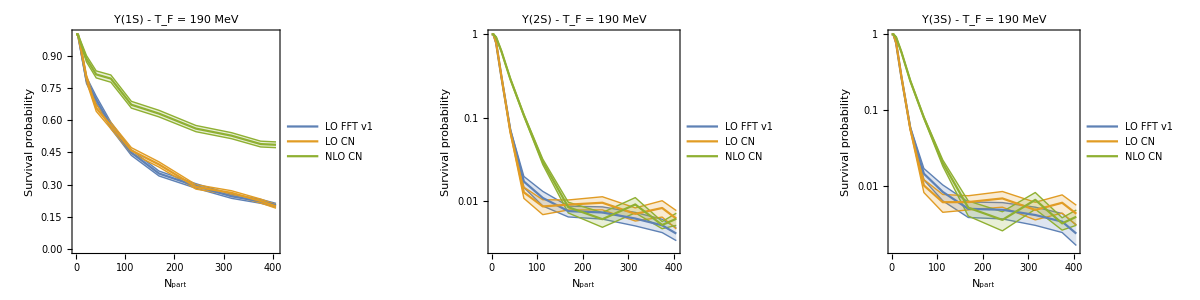

```mathematica
p1=ListPlot[{resSwave0190 [[1]],resSwave1190 [[1]],resSwave2190 [[1]]},Joined->True,IntervalMarkers->"Bands",PlotLegends->Placed[LineLegend[{"LO FFT v1","LO CN","NLO CN"},LegendMargins->20,LabelStyle->16],{Right,Top}],FrameLabel->{"N_part","Survival probability"},PlotLabel->Style["Υ(1S) - T_F = 190 MeV",18]];
p2=ListLogPlot[{resSwave0190 [[2]],resSwave1190  [[2]],resSwave2190 [[2]]},Joined->True,IntervalMarkers->"Bands",PlotLegends->Placed[LineLegend[{"LO FFT v1","LO CN","NLO CN"},LegendMargins->20,LabelStyle->16],{Right,Top}],FrameLabel->{"N_part","Survival probability"},PlotLabel->Style["Υ(2S) - T_F = 190 MeV",18]];
p3=ListLogPlot[{resSwave0190 [[3]],resSwave1190 [[3]],resSwave2190 [[3]]},Joined->True,IntervalMarkers->"Bands",PlotLegends->Placed[LineLegend[{"LO FFT v1","LO CN","NLO CN"},LegendMargins->20,LabelStyle->16],{Right,Top}],FrameLabel->{"N_part","Survival probability"},PlotLabel->Style["Υ(3S) - T_F = 190 MeV",18]];
Grid[{{p1,p2,p3}}]
```

#### KCGC - 150

```mathematica
resSwave1150  = computeSwaveRAA[{"/input/kcgc-150/output-LO/"}]
resSwave2150  = computeSwaveRAA[{"/input/kcgc-150/output-NLO/"}]
```

{{{0,1},{3.80953,0.8870.014},{9.66779,0.8140.017},{21.2928,0.6990.016},{41.0509,0.5880.015},{70.7871,0.4780.013},{112.39,0.3630.012},{168.503,0.2870.010},{243.538,0.2360.009},{315.859,0.1820.008},{374.988,0.1500.008},{406.122,0.1500.008}},{{0,1},{3.80953,0.5780.009},{9.66779,0.14210.0032},{21.2928,0.03100.0028},{41.0509,0.01950.0025},{70.7871,0.00820.0015},{112.39,0.00650.0018},{168.503,0.001560.00031},{243.538,0.00460.0017},{315.859,0.00150.0005},{374.988,0.00150.0009},{406.122,0.000840.00017}},{{0,1},{3.80953,0.5440.008},{9.66779,0.13170.0030},{21.2928,0.03180.0022},{41.0509,0.01460.0021},{70.7871,0.00600.0014},{112.39,0.00530.0015},{168.503,0.00160.0007},{243.538,0.00320.0012},{315.859,0.00120.0005},{374.988,0.00100.0007},{406.122,0.00070.0004}}}

{{{0,1},{3.80953,0.9370.013},{9.66779,0.8580.017},{21.2928,0.7870.017},{41.0509,0.7100.017},{70.7871,0.6340.016},{112.39,0.5780.015},{168.503,0.4770.013},{243.538,0.4400.013},{315.859,0.3950.012},{374.988,0.3460.011},{406.122,0.3460.011}},{{0,1},{3.80953,0.9240.013},{9.66779,0.5450.011},{21.2928,0.1610.004},{41.0509,0.03150.0024},{70.7871,0.01000.0005},{112.39,0.00800.0005},{168.503,0.003250.00010},{243.538,0.001890.00007},{315.859,0.001560.00005},{374.988,0.001350.00005},{406.122,0.001360.00005}},{{0,1},{3.80953,0.9000.012},{9.66779,0.4280.008},{21.2928,0.09810.0026},{41.0509,0.02470.0019},{70.7871,0.01030.0009},{112.39,0.00600.0010},{168.503,0.001740.00008},{243.538,0.001120.00006},{315.859,0.001170.00010},{374.988,0.001030.00010},{406.122,0.000970.00007}}}

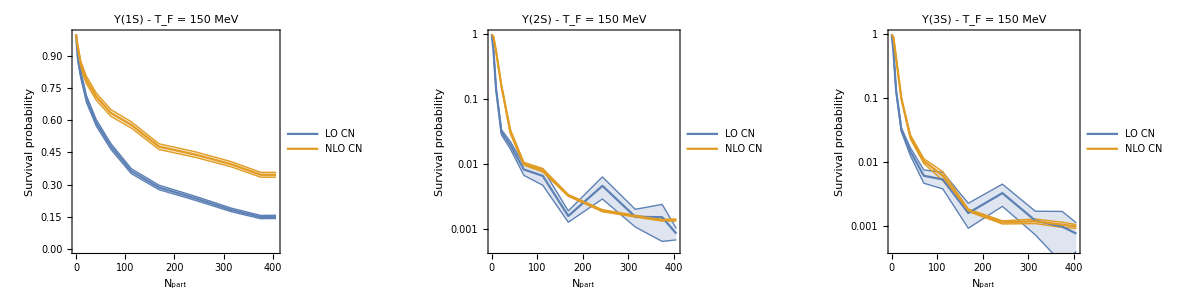

```mathematica
p1=ListPlot[{resSwave1150[[1]],resSwave2150[[1]]},Joined->True,IntervalMarkers->"Bands",PlotLegends->Placed[LineLegend[{"LO CN","NLO CN"},LegendMargins->20,LabelStyle->16],{Right,Top}],FrameLabel->{"N_part","Survival probability"},PlotLabel->Style["Υ(1S) - T_F = 150 MeV",18]];
p2=ListLogPlot[{resSwave1150[[2]],resSwave2150[[2]]},Joined->True,IntervalMarkers->"Bands",PlotLegends->Placed[LineLegend[{"LO CN","NLO CN"},LegendMargins->20,LabelStyle->16],{Right,Top}],FrameLabel->{"N_part","Survival probability"},PlotLabel->Style["Υ(2S) - T_F = 150 MeV",18]];
p3=ListLogPlot[{resSwave1150[[3]],resSwave2150[[3]]},Joined->True,IntervalMarkers->"Bands",PlotLegends->Placed[LineLegend[{"LO CN","NLO CN"},LegendMargins->20,LabelStyle->16],{Right,Top}],FrameLabel->{"N_part","Survival probability"},PlotLabel->Style["Υ(3S) - T_F = 150 MeV",18]];
Grid[{{p1,p2,p3}}]
```

## Comparisons

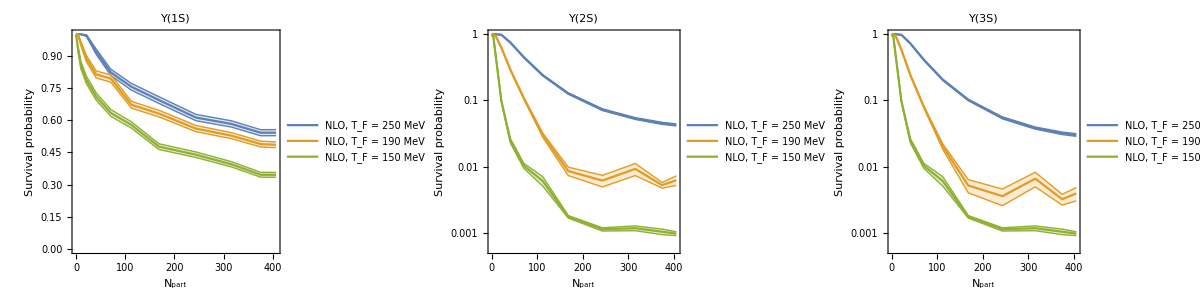

```mathematica
p1=ListPlot[{resSwave2[[1]],resSwave2190 [[1]],resSwave2150 [[1]]},Joined->True,IntervalMarkers->"Bands",PlotLegends->Placed[LineLegend[{"NLO, T_F = 250 MeV","NLO, T_F = 190 MeV","NLO, T_F = 150 MeV"},LegendMargins->20,LabelStyle->15],{Right,Top}],FrameLabel->{"N_part","Survival probability"},PlotLabel->Style["Υ(1S)",18]];
p2=ListLogPlot[{resSwave2[[2]],resSwave2190 [[2]],resSwave2150 [[3]]},Joined->True,IntervalMarkers->"Bands",PlotLegends->Placed[LineLegend[{"NLO, T_F = 250 MeV","NLO, T_F = 190 MeV","NLO, T_F = 150 MeV"},LegendMargins->20,LabelStyle->15],{Right,Top}],FrameLabel->{"N_part","Survival probability"},PlotLabel->Style["Υ(2S)",18]];
p3=ListLogPlot[{resSwave2[[3]],resSwave2190 [[3]],resSwave2150 [[3]]},Joined->True,IntervalMarkers->"Bands",PlotLegends->Placed[LineLegend[{"NLO, T_F = 250 MeV","NLO, T_F = 190 MeV","NLO, T_F = 150 MeV"},LegendMargins->20,LabelStyle->15],{Right,Top}],FrameLabel->{"N_part","Survival probability"},PlotLabel->Style["Υ(3S)",18]];
Grid[{{p1,p2,p3}}]
```

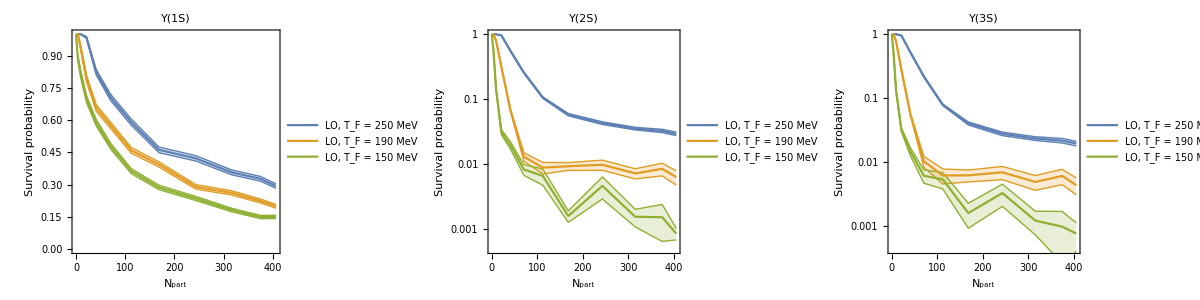

```mathematica
p1=ListPlot[{resSwave1[[1]],resSwave1190 [[1]],resSwave1150 [[1]]},Joined->True,IntervalMarkers->"Bands",PlotLegends->Placed[LineLegend[{"LO, T_F = 250 MeV","LO, T_F = 190 MeV","LO, T_F = 150 MeV"},LegendMargins->20,LabelStyle->16],{Right,Top}],FrameLabel->{"N_part","Survival probability"},PlotLabel->Style["Υ(1S)",18]];
p2=ListLogPlot[{resSwave1[[2]],resSwave1190 [[2]],resSwave1150 [[2]]},Joined->True,IntervalMarkers->"Bands",PlotLegends->Placed[LineLegend[{"LO, T_F = 250 MeV","LO, T_F = 190 MeV","LO, T_F = 150 MeV"},LegendMargins->20,LabelStyle->16],{Right,Top}],FrameLabel->{"N_part","Survival probability"},PlotLabel->Style["Υ(2S)",18]];
p3=ListLogPlot[{resSwave1[[3]],resSwave1190 [[3]],resSwave1150 [[3]]},Joined->True,IntervalMarkers->"Bands",PlotLegends->Placed[LineLegend[{"LO, T_F = 250 MeV","LO, T_F = 190 MeV","LO, T_F = 150 MeV"},LegendMargins->20,LabelStyle->16],{Right,Top}],FrameLabel->{"N_part","Survival probability"},PlotLabel->Style["Υ(3S)",18]];
Grid[{{p1,p2,p3}}]
```

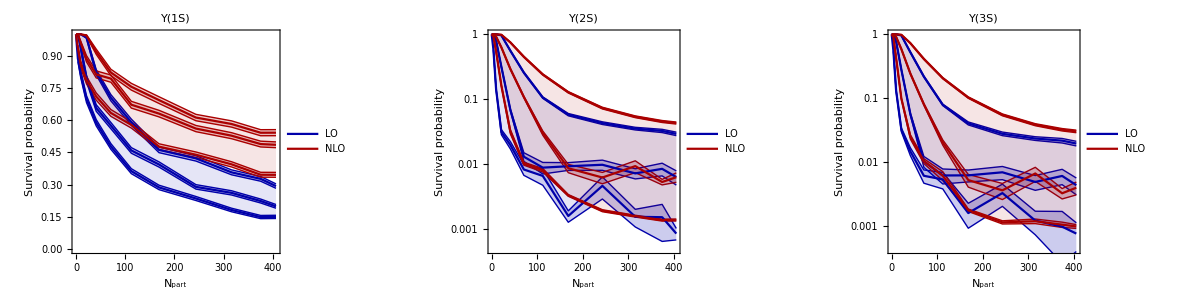

```mathematica
plotState[i_]:=ListPlot[{resSwave1[[i]],resSwave1190[[i]],resSwave1150[[i]],resSwave2 [[i]],resSwave2190 [[i]],resSwave2150 [[i]]},Joined->True,IntervalMarkers->"Bands",PlotLegends->Placed[LineLegend[{None,"LO",None,None,"NLO",None},LegendMargins->20,LabelStyle->16],{Right,Top}],FrameLabel->{"N_part","Survival probability"},PlotLabel->Style["Υ("<>ToString[i]<>"S)",18],Filling->{1->{{3},Directive[Opacity[0.1],Darker[Blue]]},4->{{6},Directive[Opacity[0.1],Darker[Red]]}},IntervalMarkersStyle->Darker/@{Blue,Blue,Blue,Red,Red,Red},PlotStyle->Darker/@{Blue,Blue,Blue,Red,Red,Red}]
plotStateLog[i_]:=ListLogPlot[{resSwave1[[i]],resSwave1190[[i]],resSwave1150[[i]],resSwave2 [[i]],resSwave2190 [[i]],resSwave2150 [[i]]},Joined->True,IntervalMarkers->"Bands",PlotLegends->Placed[LineLegend[{None,"LO",None,None,"NLO",None},LegendMargins->20,LabelStyle->16],{Right,Top}],FrameLabel->{"N_part","Survival probability"},PlotLabel->Style["Υ("<>ToString[i]<>"S)",18],Filling->{1->{{3},Directive[Opacity[0.1],Darker[Blue]]},4->{{6},Directive[Opacity[0.1],Darker[Red]]}},IntervalMarkersStyle->Darker/@{Blue,Blue,Blue,Red,Red,Red},PlotStyle->Darker/@{Blue,Blue,Blue,Red,Red,Red}]
Grid[{{plotState[1],plotStateLog[2],plotStateLog[3]}}]
```

{{0,1},{3.80953,1.0000000000014},{9.66779,1.0000000000014},{21.2928,0.9780.005},{41.0509,0.6780.015},{70.7871,0.3630.011},{112.39,0.1780.006},{168.503,0.1240.006},{243.538,0.1010.006},{315.859,0.0980.006},{374.988,0.0980.007},{406.122,0.0990.007}}

{{0,1},{3.80953,1.0000000000014},{9.66779,0.8510.013},{21.2928,0.3970.011},{41.0509,0.1040.004},{70.7871,0.02240.0035},{112.39,0.0190.004},{168.503,0.02330.0033},{243.538,0.0330.006},{315.859,0.0270.005},{374.988,0.0370.008},{406.122,0.0310.008}}

{{0,1},{3.80953,0.6510.014},{9.66779,0.1750.005},{21.2928,0.0440.004},{41.0509,0.0330.004},{70.7871,0.01710.0032},{112.39,0.0180.005},{168.503,0.00540.0011},{243.538,0.0190.007},{315.859,0.00830.0026},{374.988,0.0100.006},{406.122,0.00560.0012}}

{{0,1},{3.80953,1.0000000000014},{9.66779,1.0000000000014},{21.2928,0.9900.005},{41.0509,0.8160.015},{70.7871,0.5460.014},{112.39,0.3170.009},{168.503,0.1830.006},{243.538,0.1180.005},{315.859,0.0910.004},{374.988,0.0830.004},{406.122,0.07860.0035}}

{{0,1},{3.80953,1.0000000000014},{9.66779,0.9610.013},{21.2928,0.7100.017},{41.0509,0.3590.010},{70.7871,0.1360.005},{112.39,0.04450.0035},{168.503,0.01350.0020},{243.538,0.01090.0022},{315.859,0.0170.004},{374.988,0.01070.0011},{406.122,0.01280.0022}}

{{0,1},{3.80953,0.9860.019},{9.66779,0.6350.017},{21.2928,0.2050.007},{41.0509,0.04430.0035},{70.7871,0.01580.0009},{112.39,0.01380.0009},{168.503,0.006820.00028},{243.538,0.004290.00020},{315.859,0.003940.00018},{374.988,0.003900.00019},{406.122,0.003920.00019}}

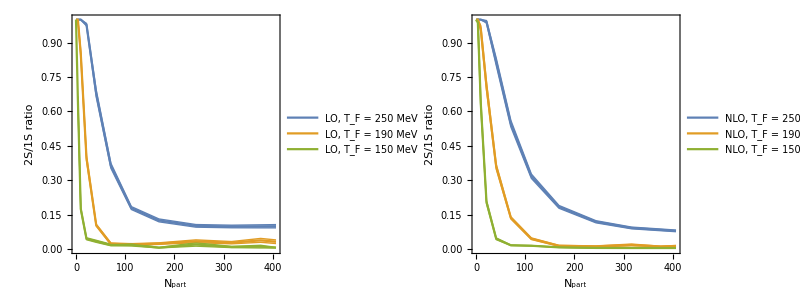

```mathematica
ratio2S1S250lo=Transpose[{resSwave1[[1]][[All,1]],resSwave1[[2]][[All,2]]/resSwave1 [[1]][[All,2]]}]
ratio2S1S190lo=Transpose[{resSwave1190 [[1]][[All,1]],resSwave1190 [[2]][[All,2]]/resSwave1190 [[1]][[All,2]]}]
ratio2S1S150lo=Transpose[{resSwave1150 [[1]][[All,1]],resSwave1150 [[2]][[All,2]]/resSwave1150 [[1]][[All,2]]}]
p1=ListPlot[{ratio2S1S250lo,ratio2S1S190lo,ratio2S1S150lo},Joined->True,IntervalMarkers->"Bands",PlotLegends->Placed[LineLegend[{"LO, T_F = 250 MeV ","LO, T_F = 190 MeV","LO, T_F = 150 MeV"},LegendMargins->20,LabelStyle->16],{Right,Top}],FrameLabel->{"N_part","2S/1S ratio"}];
ratio2S1S250nlo=Transpose[{resSwave2 [[1]][[All,1]],resSwave2[[2]][[All,2]]/resSwave2 [[1]][[All,2]]}]
ratio2S1S190nlo=Transpose[{resSwave2190 [[1]][[All,1]],resSwave2190 [[2]][[All,2]]/resSwave2190 [[1]][[All,2]]}]
ratio2S1S150nlo=Transpose[{resSwave2150 [[1]][[All,1]],resSwave2150 [[2]][[All,2]]/resSwave2150 [[1]][[All,2]]}]
p2=ListPlot[{ratio2S1S250nlo,ratio2S1S190nlo,ratio2S1S150nlo},Joined->True,IntervalMarkers->"Bands",PlotLegends->Placed[LineLegend[{"NLO, T_F = 250 MeV ","NLO, T_F = 190 MeV","NLO, T_F = 150 MeV"},LegendMargins->20,LabelStyle->16],{Right,Top}],FrameLabel->{"N_part","2S/1S ratio"}];
Grid[{{p1,p2}}]
```

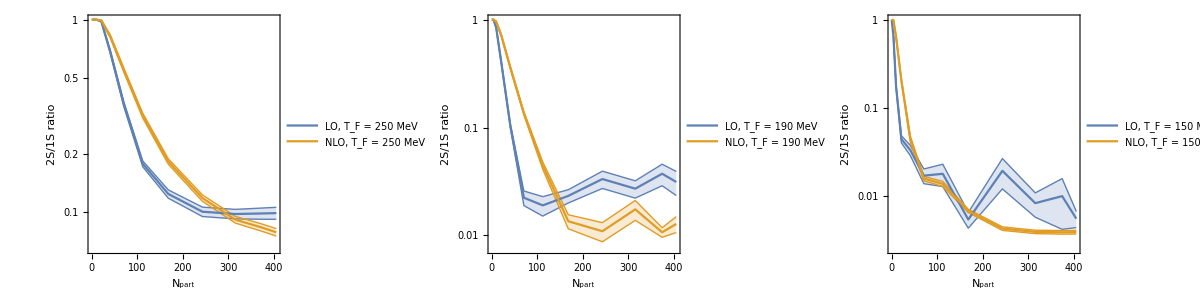

```mathematica
p1=ListLogPlot[{ratio2S1S250lo,ratio2S1S250nlo},Joined->True,IntervalMarkers->"Bands",PlotLegends->Placed[LineLegend[{"LO, T_F = 250 MeV ","NLO, T_F = 250 MeV"},LegendMargins->20,LabelStyle->16],{Right,Top}],FrameLabel->{"N_part","2S/1S ratio"}];
p2=ListLogPlot[{ratio2S1S190lo,ratio2S1S190nlo},Joined->True,IntervalMarkers->"Bands",PlotLegends->Placed[LineLegend[{"LO, T_F = 190 MeV ","NLO, T_F = 190 MeV"},LegendMargins->20,LabelStyle->16],{Right,Top}],FrameLabel->{"N_part","2S/1S ratio"}];
p3=ListLogPlot[{ratio2S1S150lo,ratio2S1S150nlo},Joined->True,IntervalMarkers->"Bands",PlotLegends->Placed[LineLegend[{"LO, T_F = 150 MeV ","NLO, T_F = 150 MeV"},LegendMargins->20,LabelStyle->16],{Right,Top}],FrameLabel->{"N_part","2S/1S ratio"}];
Grid[{{p1,p2,p3}}]
```